```mathematica
(*the only executable cell is the last one*)
```

For the model 
V(ϕ)=γ ϕ^n
the initial conditions are
Hi→(2 √As M^2 n π)/ϕi,γ→12 As M^6 n^2 π^2 ϕi^(-2-n),OverDot[ϕi]→-(2 √As M^4 n^2 π)/ϕi^2
where ϕi is the initial value of the inflaton, As is  the scalar amplitude, and M is the Planck mass.
After solving the featureless background equations, I find ϕ0 using 
t0 = FindRoot[H[t] a[t] == k0]
where the feature scale is k0=1.13*10^-3 Mpc^-1 and then setting ϕ0 = ϕ[t0].
Then I solve the feature background equations
V(ϕ)=γ ϕ^n+λ Exp[-((ϕ-ϕ0)/σ)^2.]
The value of the parameters are:

```mathematica
{n,As,ϕi,M}
{k0,ϕ0,λ,σ}
```

{2.,2.19551×10^-9,16.0257,1.}

```mathematica
{0.00113,15.609751692623052,-1.12*^-12,0.053}
```

```mathematica
-2Sqrt[2.19551*10^(-9)]*(2.44*10^(18))^2*4*π/16.02569365559123^2
-2√(2.19551*10^(-9))*4*π/16.02569365559123^2
12 As M^6 n^2 π^2 ϕi^(-2-n)
```

-2.72994×10^31

-4.58536×10^-6

```mathematica
12 2.1955111882664715*^-9 2^2 π^2 16.02569365559123^(-2-2)
12 2.1955111882664715*^-9 *(2.44*^18)^6 *2^2* π^2 *(2.44*10^18 16.02569365559123)^-4
```

1.57692×10^-11

9.38834×10^25

```mathematica
1.576918655358219*^-11*(2.44*^18)^2
```

9.38834×10^25

I have calculated the spectrum of

```mathematica
Subscript[P, Q](k) =(ϕ' (τ(k)))/(a(τ(k))H(τ(k)))Subscript[P, R](k)
```

where a is the scale factor, primes are derivates with respect to conformal time, and τ(k)=-1/k is the horizon conformal time.
The interval values for the scale k are given in terms of k0 by
intls1 = Table[k, {k, 0.04, 0.2, 0.001}];
intls2 = Table[k, {k, 0.21, 1., 0.005}];
intss1 = Table[k, {k, 1.1, 20., 0.2}];
intss2 = Table[k, {k, 21., 105., 1.}];

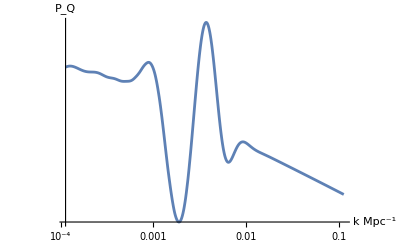

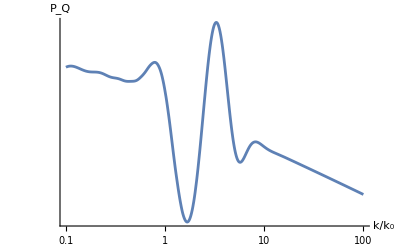

```mathematica
k0=1.13*10^-3.(*Mpc^-1*);
PQint=Interpolation[Import["TablePQm1.dat"]];
LogLogPlot[{PQint[k/k0]},{k,10^-1. k0,10^(+2.)k0},AxesLabel->{Style["k Mpc^-1",12],Style[Subscript[P,Q],16]},PlotRange->All]
LogLogPlot[{PQint[k]},{k,10^-1.,10^(+2.)},AxesLabel->{Style["k/k_0",14],Style[Subscript[P,Q],16]},PlotRange->All]
```

```mathematica
(-4.585364837378086*^-6)^2/(-4.585364837378086*^-6 16.02569365559123)
```

-2.86126×10^-7